```mathematica
Reduce[Sqrt[250*c]>1/(3/10),c]
```

c>2/45

```mathematica
Reduce[Sqrt[250*c]>1/(0.3),c]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

c>0.0444444

```mathematica
2/45//N
```

0.0444444

## Question 2 Part 1- Dampened oscillations

```mathematica
Solve[0==(b-d)x(1-x/k)-a*x*y,y]
```

{{y→((b-d) (k-x))/(a k)}}

```mathematica
Solve[0==α*ϵ*x*y-m*y,y]
```

{{y→0}}

```mathematica
Solve[0==(b-d)x(1-x/k)-α*x*y&& 0==α*ϵ*x*y-m*y,{x,y}]
```

{{x→m/(α ϵ),y→((b-d) (-m+k α ϵ))/(k α^2 ϵ)},{x→0,y→0},{x→k,y→0}}

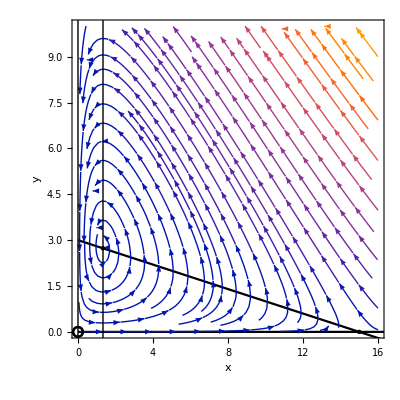

```mathematica
Show[{Plot[{((2-0.5) (15-x))/(0.5 15),0},{x,0,30},Epilog->{(*add vertical lines*)InfiniteLine[{0,0},{0,1}],InfiniteLine[{0.6/(0.9*0.5),0},{0,1}]},PlotStyle->Black,Frame->True,FrameLabel->{"x","y"}],ListPlot[List/@{{0.6/(0.5 0.9),((2-0.5) (-0.6+15 0.5 0.9))/(15 0.5^2 0.9)},{0,0},{15,0}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{None,{Graphics[Circle[]],Medium},None,{Graphics[Circle[]],Medium}}],StreamPlot[{(2-0.5)x(1-x/15)-0.5*x*y,0.5*0.9*x*y-0.6*y},{x,0,16},{y,0,10}]},PlotRange->{{0,16},{0,10}},AspectRatio->1]
```

```mathematica
ClearAll[x,y]
```

```mathematica
NDSolve[
x'[t]==(2-0.5)x[t](1-x[t]/15)-0.5*x[t]*y[t]&& 
y'[t]==0.5*0.9*x[t]*y[t]-0.6*y[t]&&
x[0]==10&&
y[0]==10,
{x,y},
{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

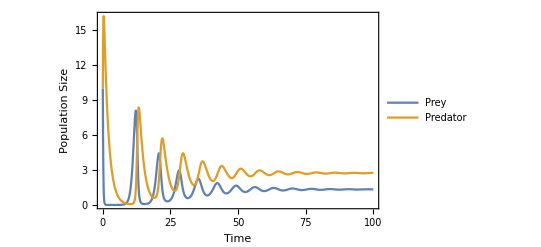

```mathematica
Plot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,100},PlotRange->All,Frame->True,FrameLabel->{"Time","Population Size"},PlotLegends->{"Prey","Predator"}]
```

## Question 2 Part 2-Stable Oscillations

Find Isoclines

```mathematica
Solve[0==n(a-b*p),p]
```

{{p→a/b}}

```mathematica
Solve[0==n(a-b*p),n]
```

{{n→0}}

```mathematica
Solve[0==p(c*n-d),p]
```

{{p→0}}

```mathematica
Solve[0==p(c*n-d),n]
```

{{n→d/c}}

Find equilibria

```mathematica
Solve[0==n(a-b*p)&& 0==p(c*n-d),{n,p}]
```

{{n→0,p→0},{n→d/c,p→a/b}}

a=2, b=1, c=0.9, d=0.5

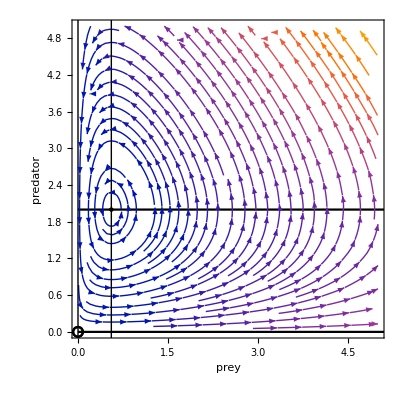

```mathematica
Show[{Plot[{2/1,0},{x,0,30},Epilog->{(*add vertical lines*)InfiniteLine[{0,0},{0,1}],InfiniteLine[{0.5/0.9,0},{0,1}]},PlotStyle->Black,Frame->True,FrameLabel->{"prey","predator"}],ListPlot[List/@{{0.5/0.9,2/1},{0,0}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{None,{Graphics[Circle[]],Medium}}],StreamPlot[{n(2-1*p),p(0.9*n-0.5)},{n,0,5},{p,0,5}]},PlotRange->{{0,5},{0,5}},AspectRatio->1]
```

```mathematica
NDSolve[
n'[t]==n[t](2-1*p[t])&& 
p'[t]==p[t](0.9*n[t]-0.5)&&
n[0]==5&&
p[0]==2,
{n,p},
{t,0,100}]
```

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

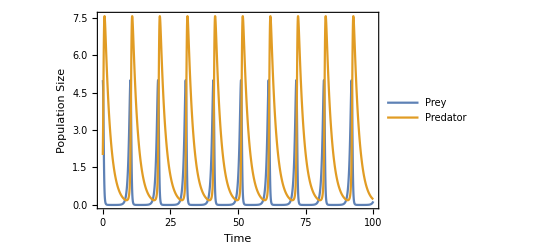

```mathematica
Plot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,100},PlotRange->All,Frame->True,FrameLabel->{"Time","Population Size"},PlotLegends->{"Prey","Predator"}]
```

## Question 2 Part 3- Competition

```mathematica
Solve[0==n1(r1-a11*n1-a12*n2),n2]
```

{{n2→(-a11 n1+r1)/a12}}

```mathematica
Solve[0==n1(r1-a11*n1-a12*n2),n1]
```

{{n1→0},{n1→(-a12 n2+r1)/a11}}

```mathematica
Solve[0==n2(r2-a22*n2-a21*n1),n2]
```

{{n2→0},{n2→(-a21 n1+r2)/a22}}

```mathematica
Solve[0==n2(r2-a22*n2-a21*n1),n1]
```

{{n1→(-a22 n2+r2)/a21}}

```mathematica
Solve[0==n1(r1-a11*n1-a12*n2)&&0==n2(r2-a22*n2-a21*n1),{n1,n2}]
```

{{n1→0,n2→r2/a22},{n1→-(a22 r1-a12 r2)/(a12 a21-a11 a22),n2→-(-a21 r1+a11 r2)/(a12 a21-a11 a22)},{n1→0,n2→0},{n1→r1/a11,n2→0}}

r1= 2, a11=0.5, a12=0.7, 
r2=2, a22 =0.6, a21 = 0.8

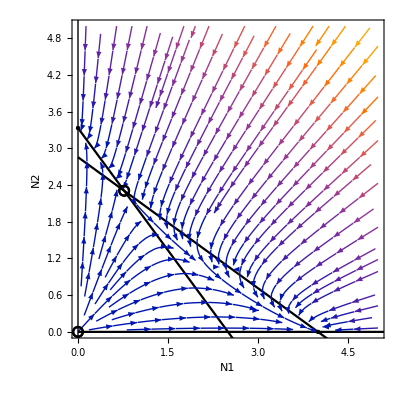

```mathematica
Show[{Plot[{(-0.5* n1+2)/0.7,0,(-0.8* n1+2)/0.6},{n1,0,30},Epilog->{(*add vertical lines*)InfiniteLine[{0,0},{0,1}]},PlotStyle->Black,Frame->True,FrameLabel->{"N1","N2"}],ListPlot[List/@{{0,2/0.6},{2/0.5,0},{-(0.6 *2-0.7* 2)/(0.7* 0.8-0.5* 0.6),-(-0.8* 2+0.5* 2)/(0.7* 0.8-0.5* 0.6)},{0,0}},PlotStyle->Directive[Black,PointSize[Large]],PlotMarkers->{None,None,{Graphics[Circle[]],Medium},{Graphics[Circle[]],Medium}}],StreamPlot[{n1(2-0.5*n1-0.7*n2),n2(2-0.6*n2-0.8*n1)},{n1,0,5},{n2,0,5}]},PlotRange->{{0,5},{0,5}},AspectRatio->1]
```

```mathematica
FullSimplify[{(0.6 *2-0.7* 2)/(0.7* 0.8-0.5* 0.6),(-0.8* 2+0.6* 2)/(0.7* 0.8-0.5* 0.6)}]
```

{-0.769231,-1.53846}